```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BS.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\SABR.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\NumericalIntegration.m"
```

```mathematica
HaganVol[S_,K_,T_,α_,β_,ρ_,ν_]:=Module[{ζ=ν/α Log[S/K],x},x=Log[(√(1-2ρ ζ+ζ^2)-ρ+ζ)/(1-ρ)];α(ζ/x)(1+(1/4 ρ α ν+1/24(2-3 ρ^2)ν^2)T)]
```

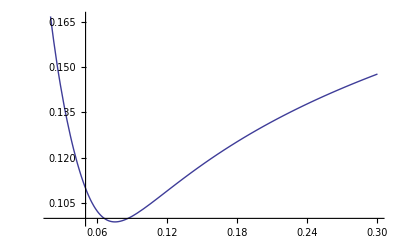

```mathematica
Module[{S=0.05,T=1,α=0.11,β=0.7,ρ=-0.5,ν=0.2},Plot[HaganVol[S,K,T,α,β,ρ,ν],{K,0.02,0.3}]]
```

```mathematica
SABROptionHaganPure[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,x,Effetmat,vol},z=(f^(1-β)-K^(1-β))/(α (1-β));
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
Effetmat=(1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T)/(1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920);
vol=If[z==0,K^(-1+β) α Effetmat,
α/(f K)^((1-β)/2) z/x  Effetmat  ];
BS[f,K,T,vol ]]
```

```mathematica
SABRVolDirectPure[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
If[z==0,θ=1;sig=K^(-1+β) α(1-2 T(K^(2 β) α^2 (-1+β)^2+K^2 ν (6 b1 α ρ+ν (2-3 ρ^2)))/(24 K^2))^(-1/2),
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z];
sig=Log[f/K]/z ξ/(ν x)(1-2 T((θ-Log[(Log[f/K] √(f K))/(f-K)])/x^2))^(-1/2)]];
```

```mathematica
SABROptionDirectPure[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
If[z==0,θ=1;sig=K^(-1+β) α(1-2 T(K^(2 β) α^2 (-1+β)^2+K^2 ν (6 b1 α ρ+ν (2-3 ρ^2)))/(24 K^2))^(-1/2),
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z];
sig=Log[f/K]/z ξ/(ν x)(1-2 T((θ-Log[(Log[f/K] √(f K))/(f-K)])/x^2))^(-1/2)];
BS[f,K,T,sig ]];
```

```mathematica
SABROptionAnalyticPure[f_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
If[z==0,θ=0,
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z]];
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
σ=α f^(β-1);
b=Abs[x];
a=√-κ;
If[z==0,call=(K^β α)/(2 √(2 π)) Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))],
  call=N[Max[f-K,0]+(f-K)/(2 √(2π))E^θ/x Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]]]];
```

```mathematica
SABRVolStrikeCuterPure[f_,α_,β_,ρ_,ν_,K1_,T_,zerocuterKb_,αp_]:=
Module[{K},
K=UnitStep[K1-zerocuterKb]K1+(UnitStep[zerocuterKb-K1]) zerocuterKb(1+αp Tanh[(K1-zerocuterKb)/(αp zerocuterKb)]);
SABROptionHaganPure[f,α,β,ρ,ν,K,T]
]
```

```mathematica
SABRVolStrikeCuterPure[f_,α_,β_,ρ_,ν_,K1_,T_,ϵ_]:=
Module[{K},
K=K1+ϵ ⅇ^(-K1/ϵ);
SABROptionHaganPure[f,α,β,ρ,ν,K,T]
]
```

```mathematica
SABROptionStrikeCuterPure[f_,α_,β_,ρ_,ν_,K1_,T_,zerocuterKb_,αp_]:=
Module[{K},
K=UnitStep[K1-zerocuterKb]K1+(UnitStep[zerocuterKb-K1]) zerocuterKb(1+αp Tanh[(K1-zerocuterKb)/(αp zerocuterKb)]);
SABROptionDirectPure[f,α,β,ρ,ν,K,T]
]
```

```mathematica
SABROptionStrikeCuterPure[f_,α_,β_,ρ_,ν_,K1_,T_,ϵ_]:=
Module[{K},
K=K1+ϵ ⅇ^(-K1/ϵ);
SABROptionDirectPure[f,α,β,ρ,ν,K,T]
]
```

```mathematica
SABROptionStrikeCuterPure1[f_,α_,β_,ρ_,ν_,K1_,T_]:=
SABROptionStrikeCuterPure[f,α,β,ρ,ν,K1,T,0.3,1.5]
```

```mathematica
SABROptionStrikeCuterPure2[f_,α_,β_,ρ_,ν_,K1_,T_]:=
SABROptionStrikeCuterPure[f,α,β,ρ,ν,K1,T,0.03]
```

```mathematica
Module[{S=0.05,T=1,α=0.11,β=0.7,ρ=-0.5,ν=0.2,σ},σ=SABRVolDirectPure[S,α,β,ρ,ν,S,T];
ComputeAlphaSABROptionAnalytic[S,σ,β,ρ,ν,T]]
```

0.11

```mathematica
ComputeAlphaSABROptionAnalytic[f_,ATMvol_,β_,ρ_,ν_,T_]:=NewtonFindRoot[(SABRVolDirectPure[f,#,β,ρ,ν,f,T]-ATMvol)&,0.05,0.01,0.00001,10][[1]]
```

```mathematica
NormDis[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
BS[f_,k_,t_,v_]:= f  NormDis[(Log[f/k]+(v^2 t)/2)/(v Sqrt[t])]-k  NormDis[(Log[f/k]-(v^2 t)/2)/(v Sqrt[t])]
```

(σ^2)_Dupire=(2(∂C)/(∂T))/(K^2(∂C)/(∂K))

```mathematica
DupireVolGeneric[S_,k_,T_,α_,β_,ρ_,v_]:=Module[{Calendar=(ⅇ^(-Log[S/k]^2/(2 T v[k,T]^2)-1/8 T v[k,T]^2) √(S/k) k √T Derivative[0,1][v][k,T])/(√(2 π)),
cspread=1/2 (-1+Erf[(-2 Log[S/k]+T v[k,T]^2)/(2 √2 √T v[k,T])])+(ⅇ^(-Log[S/k]^2/(2 T v[k,T]^2)-1/8 T v[k,T]^2) √(S/k) k √T Derivative[1,0][v][k,T])/(√(2 π))},2 Calendar/(k^2 cspread)]
```

```mathematica
SABRDensity1[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{kshift=Max[S,k]/100},
(SABROptionHaganPure[S,α,β,ρ,ν,k+kshift,T]+SABROptionHaganPure[S,α,β,ρ,ν,k-kshift,T]-2SABROptionHaganPure[S,α,β,ρ,ν,k,T])/kshift^2]
```

```mathematica
SABRDensity2[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{kshift=Max[S,k]/100},
(SABRVolDirectPure[S,α,β,ρ,ν,k+kshift,T]+SABRVolDirectPure[S,α,β,ρ,ν,k-kshift,T]-2SABRVolDirectPure[S,α,β,ρ,ν,k,T])/kshift^2]
```

```mathematica
SABRDensity3[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{kshift=Max[S,k]/100},
(SABROptionAnalyticPure[S,α,β,ρ,ν,k+kshift,T]+SABROptionAnalyticPure[S,α,β,ρ,ν,k-kshift,T]-2SABROptionAnalyticPure[S,α,β,ρ,ν,k,T])/kshift^2]
```

```mathematica
SABRDensity4[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{kshift=Max[S,k]/100},
(SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k+kshift,T]+SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k-kshift,T]-2SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k,T])/kshift^2]
```

```mathematica
SABRDensity5[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{kshift=Max[S,k]/100},
(SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k+kshift,T]+SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k-kshift,T]-2SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k,T])/kshift^2]
```

```mathematica
SABRTheta1[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Tshift=0.001},
(SABROptionHaganPure[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionHaganPure[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift]
```

```mathematica
SABRTheta2[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Tshift=0.001},
(SABRVolDirectPure[S,α,β,ρ,ν,k,T+Tshift/2]-SABRVolDirectPure[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift]
```

```mathematica
SABRTheta3[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Tshift=0.001},
(SABROptionAnalyticPure[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionAnalyticPure[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift]
```

```mathematica
SABRTheta4[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Tshift=0.001},
(SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift]
```

```mathematica
SABRTheta5[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Tshift=0.001},
(SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift]
```

```mathematica
DupireVolSABR1[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Calendar,cspread2,Tshift=0.001,kshift=Max[S,k]/100},
Calendar=(SABROptionHaganPure[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionHaganPure[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift;
cspread2=(SABROptionHaganPure[S,α,β,ρ,ν,k+kshift,T]+SABROptionHaganPure[S,α,β,ρ,ν,k-kshift,T]-2SABROptionHaganPure[S,α,β,ρ,ν,k,T])/kshift^2;
2 Calendar/(k^2 cspread2)]
```

```mathematica
DupireVolSABR2[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Calendar,cspread2,Tshift=0.001,kshift=Max[S,k]/100},
Calendar=(SABROptionDirectPure[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionDirectPure[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift;
cspread2=(SABROptionDirectPure[S,α,β,ρ,ν,k+kshift,T]+SABROptionDirectPure[S,α,β,ρ,ν,k-kshift,T]-2SABROptionDirectPure[S,α,β,ρ,ν,k,T])/kshift^2;
2 Calendar/(k^2 cspread2)]
```

```mathematica
DupireVolSABR3[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Calendar,cspread2,Tshift=0.001,kshift=Max[S,k]/100},
Calendar=(SABROptionAnalyticPure[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionAnalyticPure[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift;
cspread2=(SABROptionAnalyticPure[S,α,β,ρ,ν,k+kshift,T]+SABROptionAnalyticPure[S,α,β,ρ,ν,k-kshift,T]-2SABROptionAnalyticPure[S,α,β,ρ,ν,k,T])/kshift^2;
2 Calendar/(k^2 cspread2)]
```

```mathematica
DupireVolSABR4[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Calendar,cspread2,Tshift=0.001,kshift=Max[S,k]/100},
Calendar=(SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift;
cspread2=(SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k+kshift,T]+SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k-kshift,T]-2SABROptionStrikeCuterPure1[S,α,β,ρ,ν,k,T])/kshift^2;
2 Calendar/(k^2 cspread2)]
```

```mathematica
DupireVolSABR5[S_,k_,T_,α_,β_,ρ_,ν_]:=Module[{Calendar,cspread2,Tshift=0.001,kshift=Max[S,k]/100},
Calendar=(SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k,T+Tshift/2]-SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k,T-Tshift/2])/Tshift;
cspread2=(SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k+kshift,T]+SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k-kshift,T]-2SABROptionStrikeCuterPure2[S,α,β,ρ,ν,k,T])/kshift^2;
2 Calendar/(k^2 cspread2)]
```

```mathematica
Module[{S=0.05,K=0.04,T=1,α=0.11,β=0.7,ρ=-0.5,ν=0.2},DupireVolSABR3[S,K,T,α,β,ρ,ν]]
```

0.0970771

```mathematica
0.05^0.3
```

0.407091

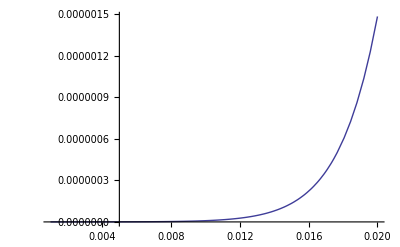

```mathematica
Module[{S=0.05,T=1,α=0.05,β=0.6,ρ=-0.01,ν=0.3},Plot[SABRTheta5[S,K,T,α,β,ρ,ν],{K,0.001,0.02},PlotRange->All]]
```

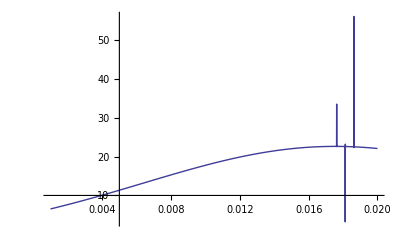

```mathematica
Module[{S=0.05,T=1,α=0.05,β=0.6,ρ=-0.01,ν=0.3},Plot[SABRDensity4[S,K,T,α,β,ρ,ν],{K,0.001,0.02},PlotRange->All]]
```

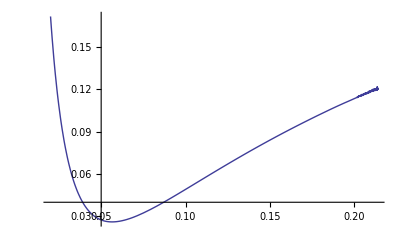

```mathematica
Module[{S=0.05,T=1,α=0.05,β=0.6,ρ=-0.01,ν=0.3},Plot[DupireVolSABR1[S,K,T,α,β,ρ,ν],{K,0.02,35α S^(β/2) ν √T}]]
```

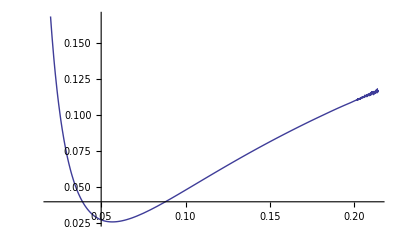

```mathematica
Module[{S=0.05,T=1,α=0.05,β=0.6,ρ=-0.01,ν=0.3},Plot[DupireVolSABR2[S,K,T,α,β,ρ,ν],{K,0.02,35α S^(β/2) ν √T}]]
```

```mathematica
DupireVolSABR3
```

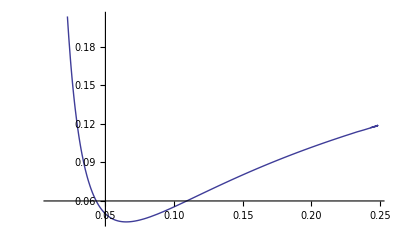

```mathematica
Module[{S=0.05,T=1,α=0.05,β=0.5,ρ=-0.01,ν=0.3},Plot[DupireVolSABR3[S,K,T,α,β,ρ,ν],{K,0.01,35α  S^(β/2) ν √T}]]
```

```mathematica
35α S^(β/2) ν √T
```

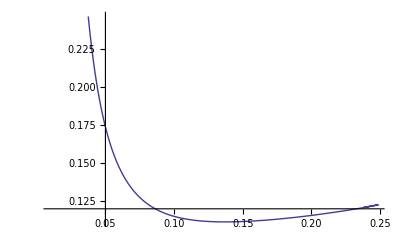

```mathematica
Module[{S=0.05,T=1,α=0.05,β=0.5,ρ=-0.01,ν=0.3},Plot[DupireVolSABR4[S,K,T,α,β,ρ,ν],{K,0.01,35α  S^(β/2) ν √T}]]
```

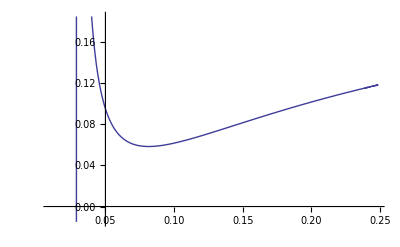

```mathematica
Module[{S=0.05,T=1,α=0.05,β=0.5,ρ=-0.01,ν=0.3},Plot[DupireVolSABR5[S,K,T,α,β,ρ,ν],{K,0.01,35α  S^(β/2) ν √T}]]
```

## Import of Data

### Chargement des smiles de CMS

```mathematica
MaturiteVec={0.25,0.5,1,2,3,4,5,7,10,12,15,20};
```

```mathematica
DateIndex=7;
```

```mathematica
Maturity=MaturiteVec[[DateIndex]]
```

5

```mathematica
SABRForward=Import["My Documents\\\Correlation_EUR\\CMSRateForward.xls"][[1]];
```

```mathematica
forwardVec={Drop[SABRForward[[6]],1][[1]],Drop[SABRForward[[6]],1][[2]],Drop[SABRForward[[6]],1][[5]],Drop[SABRForward[[6]],1][[10]],Drop[SABRForward[[6]],1][[20]],Drop[SABRForward[[6]],1][[30]]}/100
```

{0.0404819,0.0408441,0.0420872,0.0434527,0.0439235,0.043509}

```mathematica
SABRRho=Import["My Documents\\\Correlation_EUR\\rho.xls"][[1]];
SABRNu=Import["My Documents\\\Correlation_EUR\\nu.xls"][[1]];
SABRBeta=Import["My Documents\\\Correlation_EUR\\beta.xls"][[1]];

SABRATM=Import["My Documents\\\Correlation_EUR\\VolATM.xls"][[1]];
```

```mathematica
SABRRho[[8]]
```

{5.00822,0.17295,0.13985,0.00439,-0.05426,-0.08521,-0.09806}

donc c' est associé aux vecteurs :

```mathematica
rhoVec=Drop[SABRRho[[8]],1]
```

{0.17295,0.13985,0.00439,-0.05426,-0.08521,-0.09806}

```mathematica
betaVec=Drop[SABRBeta[[8]],1]
```

{0.4,0.3,0.3,0.3,0.3,0.3}

```mathematica
nuVec=Drop[SABRNu[[8]],1]
```

{0.33087,0.33882,0.33684,0.33543,0.33566,0.33363}

```mathematica
ATMVec={SABRATM[[7,2]],SABRATM[[7,3]],SABRATM[[7,6]],SABRATM[[7,11]],SABRATM[[7,13]],SABRATM[[7,15]]}/100
```

{0.152,0.156,0.16,0.149,0.134,0.131}

Determination des alpha :

```mathematica
alphaVec=Table[ComputeAlphaSABROptionAnalytic[forwardVec[[i]],ATMVec[[i]],betaVec[[i]],rhoVec[[i]],nuVec[[i]],Maturity],{i,1,6}]
```

initial x=0.05

initial fx=0.213967

new x=0.0219007

fx=0.00603809

new x=0.0210753

fx=0.0000334295

new x=0.0210707

fx=1.68842×10^-7

initial x=0.05

initial fx=0.354042

new x=0.0179721

fx=0.0221607

new x=0.0157767

fx=0.000217917

new x=0.0157551

fx=1.66308×10^-6

initial x=0.05

initial fx=0.3347

new x=0.0183083

fx=0.017315

new x=0.0165433

fx=0.000124351

new x=0.0165306

fx=7.17641×10^-7

initial x=0.05

initial fx=0.33206

new x=0.0174097

fx=0.0154916

new x=0.0157853

fx=0.0000871993

new x=0.0157761

fx=3.96698×10^-7

initial x=0.05

initial fx=0.342209

new x=0.015953

fx=0.0154096

new x=0.0143192

fx=0.0000712886

new x=0.0143116

fx=2.62787×10^-7

initial x=0.05

initial fx=0.347738

new x=0.015575

fx=0.015681

new x=0.0139206

fx=0.0000689131

new x=0.0139133

fx=2.39367×10^-7

{0.0210707,0.0157551,0.0165306,0.0157761,0.0143116,0.0139133}

### Importation de Correlation

```mathematica
Correlation3M3M=Import["My Documents\\\Correlation_EUR\\3M_3M.xls"][[1]];
Correlation3M2Y=Import["My Documents\\\Correlation_EUR\\3M_2Y.xls"][[1]];
Correlation3M5Y=Import["My Documents\\\Correlation_EUR\\3M_5Y.xls"][[1]];
Correlation3M10Y=Import["My Documents\\\Correlation_EUR\\3M_10Y.xls"][[1]];
Correlation3M20Y=Import["My Documents\\\Correlation_EUR\\3M_20Y.xls"][[1]];
Correlation3M30Y=Import["My Documents\\\Correlation_EUR\\3M_30Y.xls"][[1]];
Correlation2Y2Y=Import["My Documents\\\Correlation_EUR\\2Y_2Y.xls"][[1]];
Correlation2Y5Y=Import["My Documents\\\Correlation_EUR\\2Y_5Y.xls"][[1]];
Correlation2Y10Y=Import["My Documents\\\Correlation_EUR\\2Y_10Y.xls"][[1]];
Correlation2Y20Y=Import["My Documents\\\Correlation_EUR\\2Y_20Y.xls"][[1]];
Correlation2Y30Y=Import["My Documents\\\Correlation_EUR\\2Y_30Y.xls"][[1]];

Correlation5Y5Y=Import["My Documents\\\Correlation_EUR\\5Y_5Y.xls"][[1]];
Correlation5Y30Y=Import["My Documents\\\Correlation_EUR\\5Y_30Y.xls"][[1]];

Correlation10Y10Y=Import["My Documents\\\Correlation_EUR\\10Y_10Y.xls"][[1]];
Correlation10Y20Y=Import["My Documents\\\Correlation_EUR\\10Y_20Y.xls"][[1]];
Correlation10Y30Y=Import["My Documents\\\Correlation_EUR\\10Y_30Y.xls"][[1]];

Correlation20Y20Y=Import["My Documents\\\Correlation_EUR\\20Y_20Y.xls"][[1]];

Correlation30Y30Y=Import["My Documents\\\Correlation_EUR\\30Y_30Y.xls"][[1]];
```

### Approximation des correlations manquantes

```mathematica
Correlation5Y10Y=Correlation5Y5Y+(Correlation5Y30Y-Correlation5Y5Y)5/20;
Correlation5Y20Y=Correlation5Y5Y+(Correlation5Y30Y-Correlation5Y5Y)15/20;
Correlation20Y30Y=Correlation10Y30Y+(Correlation30Y30Y-Correlation10Y30Y)20/30;
```

Creation de la matrice de correlation

le vecteur des maturité associées est :

```mathematica
CorrelationMatrix={
{Correlation3M3M[[DateIndex,DateIndex]],Correlation3M2Y[[DateIndex,DateIndex]],Correlation3M5Y[[DateIndex,DateIndex]],Correlation3M10Y[[DateIndex,DateIndex]],Correlation3M20Y[[DateIndex,DateIndex]],Correlation3M30Y[[DateIndex,DateIndex]]},
{Correlation3M2Y[[DateIndex,DateIndex]],Correlation2Y2Y[[DateIndex,DateIndex]],Correlation2Y5Y[[DateIndex,DateIndex]],Correlation2Y10Y[[DateIndex,DateIndex]],Correlation2Y20Y[[DateIndex,DateIndex]],Correlation2Y30Y[[DateIndex,DateIndex]]},
{Correlation3M5Y[[DateIndex,DateIndex]],Correlation2Y5Y[[DateIndex,DateIndex]],Correlation5Y5Y[[DateIndex,DateIndex]],Correlation5Y10Y[[DateIndex,DateIndex]],Correlation5Y20Y[[DateIndex,DateIndex]],Correlation5Y30Y[[DateIndex,DateIndex]]},
{Correlation3M10Y[[DateIndex,DateIndex]],Correlation2Y10Y[[DateIndex,DateIndex]],Correlation5Y10Y[[DateIndex,DateIndex]],Correlation10Y10Y[[DateIndex,DateIndex]],Correlation10Y20Y[[DateIndex,DateIndex]],Correlation10Y30Y[[DateIndex,DateIndex]]},
{Correlation3M20Y[[DateIndex,DateIndex]],Correlation2Y20Y[[DateIndex,DateIndex]],Correlation5Y20Y[[DateIndex,DateIndex]],Correlation10Y20Y[[DateIndex,DateIndex]],Correlation20Y20Y[[DateIndex,DateIndex]],Correlation20Y30Y[[DateIndex,DateIndex]]},
{Correlation3M30Y[[DateIndex,DateIndex]],Correlation2Y30Y[[DateIndex,DateIndex]],Correlation5Y30Y[[DateIndex,DateIndex]],Correlation10Y30Y[[DateIndex,DateIndex]],Correlation20Y30Y[[DateIndex,DateIndex]],Correlation30Y30Y[[DateIndex,DateIndex]]}
}/100;
```

```mathematica
Eigenvalues[CorrelationMatrix]
```

{5.43173,0.443242,0.0815366,0.022768,0.013016,0.00770214}

## Optimisation

Vecteur de poid du basket :

```mathematica
Weigths={1,1,1,1,1,1};
```

```mathematica
ForwardBasket[x1_,x2_,x3_,x4_,x5_,x6_]:=Module[{xi={x1,x2,x3,x4,x5,x6}},Sum[forwardVec[[i]] ⅇ^xi[[i]] Weigths[[i]],{i,1,6}]]
```

```mathematica
p[x1_,x2_,x3_,x4_,x5_,x6_]:=Module[{y1=forwardVec[[1]] ⅇ^x1 Weigths[[1]],y2=forwardVec[[2]] ⅇ^x2 Weigths[[2]],y3=forwardVec[[3]] ⅇ^x3 Weigths[[3]],y4=forwardVec[[4]] ⅇ^x4 Weigths[[4]],y5=forwardVec[[5]] ⅇ^x5 Weigths[[5]],y6=forwardVec[[6]] ⅇ^x6 Weigths[[6]],sum},
sum=y1+y2+y3+y4+y5+y6;
{y1,y2,y3,y4,y5,y6}/sum]
```

```mathematica
p[0.1,0.1,0.1,0.1,0.1,0.1]
```

{0.15919,0.160615,0.165503,0.170873,0.172724,0.171094}

Cote droit des equations

```mathematica
eqnGauche[i_,leglst_,xi_]:=Module[{u},
CoeffBasedIntegrate[(1/DupireVolSABR1[forwardVec[[i]],forwardVec[[i]] Exp[#],Maturity,alphaVec[[i]],betaVec[[i]],rhoVec[[i]],nuVec[[i]]])&,LegendreCoeffsFromLegendre[leglst,0.,xi]]]
```

```mathematica
eqnDroite[i_,x1_,x2_,x3_,x4_,x5_,x6_]:=Module[{xi={x1,x2,x3,x4,x5,x6},p1=p[x1,x2,x3,x4,x5,x6]},Sum[CorrelationMatrix[[i,j]]p1[[j]]DupireVolSABR1[forwardVec[[j]],forwardVec[[j]] Exp[xi[[j]]],Maturity,alphaVec[[j]],betaVec[[j]],rhoVec[[j]],nuVec[[j]]],{j,1,6}]]
```

```mathematica
Module[{},eqnDroite[2,0.1,0.1,0.1,0.1,0.1,0.1]]
```

0.0167575

```mathematica
Module[{x1=0.05,leglst=LegendreCoeffs[10]},eqnGauche[2,leglst,0.1]]
```

4.64406

```mathematica
Clear[x1,x2,x3,x4,x5,x6]
```

```mathematica
Optimisep[B_]:=Module[{leglst=LegendreCoeffs[10],λini,xiini},
{xiini,λini}=ApproximatedOptimizep[B];
FindRoot[{
eqnGauche[1,leglst,x1]==λ  eqnDroite[1,x1,x2,x3,x4,x5,x6],
eqnGauche[2,leglst,x2]==λ  eqnDroite[2,x1,x2,x3,x4,x5,x6],
eqnGauche[3,leglst,x3]==λ  eqnDroite[3,x1,x2,x3,x4,x5,x6],
eqnGauche[4,leglst,x4]==λ  eqnDroite[4,x1,x2,x3,x4,x5,x6],
eqnGauche[5,leglst,x5]==λ  eqnDroite[5,x1,x2,x3,x4,x5,x6],
eqnGauche[6,leglst,x6]==λ  eqnDroite[6,x1,x2,x3,x4,x5,x6],
Sum[forwardVec[[j]] ⅇ^({x1,x2,x3,x4,x5,x6}[[j]])Weigths[[j]],{j,1,6}]==B},
{{x1,xiini[[1]]},{x2,xiini[[1]]},{x3,xiini[[1]]},{x4,xiini[[1]]},{x5,xiini[[1]]},{x6,xiini[[1]]},{λ,λini}}]]
```

```mathematica
Optimisep[B_]:=Module[{leglst=LegendreCoeffs[10],λini,xiini},
{xiini,λini}=ApproximatedOptimizep[B];
FindMinimum[
(eqnGauche[1,leglst,x1]-λ  eqnDroite[1,x1,x2,x3,x4,x5,x6])^2+
(eqnGauche[2,leglst,x2]-λ  eqnDroite[2,x1,x2,x3,x4,x5,x6])^2+
(eqnGauche[3,leglst,x3]-λ  eqnDroite[3,x1,x2,x3,x4,x5,x6])^2+
(eqnGauche[4,leglst,x4]-λ  eqnDroite[4,x1,x2,x3,x4,x5,x6])^2+
(eqnGauche[5,leglst,x5]-λ  eqnDroite[5,x1,x2,x3,x4,x5,x6])^2+
(eqnGauche[6,leglst,x6]-λ  eqnDroite[6,x1,x2,x3,x4,x5,x6])^2+
(Sum[forwardVec[[j]] ⅇ^({x1,x2,x3,x4,x5,x6}[[j]])Weigths[[j]],{j,1,6}]-B)^2,
{{x1,xiini[[1]]},{x2,xiini[[1]]},{x3,xiini[[1]]},{x4,xiini[[1]]},{x5,xiini[[1]]},{x6,xiini[[1]]},{λ,λini}},
MaxIterations->100]]
```

```mathematica
Off[Max::"nord",FindRoot::"nlnum"]
```

```mathematica
Timing[sol=Optimisep[0.25]]
```

BF=0.254298 σF=,{0.0209254,0.0218035,0.022826,0.0198233,0.0160526,0.0153707} σB0=0.0184826 xbar=-0.0170478

λ=-49.905 xi={-0.017393,-0.0193049,-0.0208155,-0.0179604,-0.0139951,-0.0131335}

equ1={-0.828735,-0.849662}
{-0.879266,-0.905614}
{-0.898233,-0.933289}
{-0.891701,-0.927697}
{-0.859728,-0.893059}
{-0.842845,-0.87535}

equ2={0.250001,0.25}

```mathematica
CheckSol[B_]:=Module[{p1,xbar,σB0,λ0,λb,σF,xi,xi2,linearized,p0,xbar0,leglst=LegendreCoeffs[10],equ1},
xi={x1,x2,x3,x4,x5,x6}//.sol;
λ0=λ //. sol;
equ1=Table[{eqnGauche[i,leglst,xi[[i]]],λ0  eqnDroite[i,xi[[1]],xi[[2]],xi[[3]],xi[[4]],xi[[5]],xi[[6]]]},{i,1,6}];
Print["equ1=",equ1// ColumnForm];
p1=p[x1,x2,x3,x4,x5,x6]//.sol;
xbar=Sum[p1[[i]] xi[[i]]//.sol,{i,1,6}];
p0=p[0,0,0,0,0,0];
σF=Table[DupireVolSABR1[forwardVec[[j]],forwardVec[[j]],Maturity,alphaVec[[j]],betaVec[[j]],rhoVec[[j]],nuVec[[j]]],{j,1,6}];
σB0=√Sum[CorrelationMatrix[[i,j]]p0[[i]]p0[[j]]σF[[i]]σF[[j]],{i,1,6},{j,1,6}];
λb=xbar/σB0^2;
xbar0=λ0 σB0^2;
xi2=Table[Sum[CorrelationMatrix[[i,j]]p0[[j]]σF[[i]]σF[[j]],{j,1,6}],{i,1,6}]λ0;
linearized=Table[Sum[CorrelationMatrix[[i,j]]p0[[j]]σF[[i]]σF[[j]],{j,1,6}],{i,1,6}];
Print["xbar=",xbar," λ0=",λ0," λb=",λb," xi2=",xi2];
]
```

```mathematica
λ eqnDroite[1,x1,x2,x3,x4,x5,x6] //. sol
```

0.0160357-0.000926949 ⅈ

```mathematica
CheckSol[0.2]
```

equ1={0.200929,0.343072-0.15043 ⅈ}
{0.102295,0.377958-0.16639 ⅈ}
{0.00796392,0.402203-0.178151 ⅈ}
{0.14823-0.00367812 ⅈ,0.409739-0.183261 ⅈ}
{0.0174779,0.398527-0.177332 ⅈ}
{0.0386574,0.39112-0.174106 ⅈ}

xbar=0.0172948 λ0=1.00168 λb=50.628 xi2={0.000349107,0.000387483,0.000417803,0.000360496,0.000280905,0.000263612}

```mathematica
ApproximatedOptimizep[B_,leglst_]:=Module[{λ,p1,xbar,BF,σB0,σF,σB01,p0,xi,egalites1,egalites2,X1,X2},
BF=Sum[forwardVec[[i]] Weigths[[i]],{i,1,6}];
σF=Table[DupireVolSABR1[forwardVec[[j]],forwardVec[[j]],Maturity,alphaVec[[j]],betaVec[[j]],rhoVec[[j]],nuVec[[j]]],{j,1,6}];
p0=p[0,0,0,0,0,0];
σB0=√Sum[CorrelationMatrix[[i,j]]p0[[i]]p0[[j]]σF[[i]]σF[[j]],{i,1,6},{j,1,6}];
xbar=Log[B/BF];
Print["BF=",BF," σF=,",σF," σB0=",σB0," xbar=",xbar];
λ=xbar/σB0^2;
xi=Table[Sum[CorrelationMatrix[[i,j]]p0[[j]]σF[[i]]σF[[j]],{j,1,6}],{i,1,6}]xbar/σB0^2;
Print["λ=",λ," xi=",xi];
egalites1=Table[{X1=eqnGauche[i,leglst,xi[[i]]],X2=λ eqnDroite[i,xi[[1]],xi[[2]],xi[[3]],xi[[4]],xi[[5]],xi[[6]]],X1-X2},{i,1,6}];
egalites2={X1=ForwardBasket[xi[[1]],xi[[2]],xi[[3]],xi[[4]],xi[[5]],xi[[6]]],X2=B,X1-X2};
Print["equ1=",egalites1// ColumnForm];
Print["equ2=",egalites2];
{xi,λ}]
```

```mathematica
NewtonFindRoot[func_,initial_,shift_,accuracy_,nbloopmax_]:=
Module[{derf,x=initial,i=0,fx},
Print["initial x=",x];
fx=func[x];
Print["initial fx=",fx];
While[(Abs[fx]>accuracy)&&(i<nbloopmax),
derf=(func[x+shift]-fx)/shift;
x-=fx/derf;
Print[" new x=",x];
i++;
fx=func[x];
Print["fx=",fx];
];
{x,i,Abs[fx]}]
```

The system to solve is :

∫_0^x_i ⅆu/σ_i[u]=λ∑_(j=1)^n ρ_ij p_j[x^*]σ_j[(x^*)_j]

∑_(i=1)^n w_i F_i ⅇ^((x^*)_i)=B

we approximate the integral by a simpson rule :

∫_0^x_i ⅆu/σ_i[u]=x_i/6(1/σ_i[0]+4/σ_i[x_i/2]+1/σ_i[x_i])

So this give us

x_i=6λ(∑_(j=1)^n ρ_ij p_j[x^*]σ_j[(x^*)_j])/(1/σ_i[0]+4/σ_i[x_i/2]+1/σ_i[x_i])

and the equations :

∑_(i=1)^n w_i F_i ⅇ^(6λ(∑_(j=1)^n ρ_ij p_j[x^*]σ_j[(x^*)_j])/(1/σ_i[0]+4/σ_i[x_i/2]+1/σ_i[x_i]))=B

```mathematica
IterationOptimizep[ruleSet_,B_,leglst_]:=Module[{λ,p1,xbar,BF,σB0,σF,σFi,σFm,σB01,pF,xi1,xi2,λ1,λ2,egalites1,egalites2,X1,X2,sol},
xi1=ruleSet[[1]];
λ1=ruleSet[[2]];
BF=Sum[forwardVec[[i]] Weigths[[i]],{i,1,6}];
pF=p[0,0,0,0,0,0];
σF=Table[DupireVolSABR1[forwardVec[[j]],forwardVec[[j]],Maturity,alphaVec[[j]],betaVec[[j]],rhoVec[[j]],nuVec[[j]]],{j,1,6}];
σFm=Table[DupireVolSABR1[forwardVec[[j]],forwardVec[[j]]Exp[xi1[[j]]/2],Maturity,alphaVec[[j]],betaVec[[j]],rhoVec[[j]],nuVec[[j]]],{j,1,6}];
σFi=Table[DupireVolSABR1[forwardVec[[j]],forwardVec[[j]]Exp[xi1[[j]]],Maturity,alphaVec[[j]],betaVec[[j]],rhoVec[[j]],nuVec[[j]]],{j,1,6}];
Print["BF=",BF," σF=,",σF," σFm=",σFm," σFi=",σFi];
Print["BF=",BF," σF=,",σF," σFm=",σFm," σFi=",σFi];
Print["BF=",BF," σF=,",σF," σFm=",σFm," σFi=",σFi];
p1=p[xi1[[1]],xi1[[2]],xi1[[3]],xi1[[4]],xi1[[5]],xi1[[6]]];
Print["p1=",p1];
sol=FindRoot[Sum[forwardVec[[i]] Weigths[[i]]Exp[2 λ/(1/σF[[i]]+1/σFi[[i]])Sum[CorrelationMatrix[[i,j]]p1[[j]]σFi[[j]],{j,1,6}]],{i,1,6}]-B==0,{λ,λ1},MaxIterations->10];
Print["sol(new λ)=",sol];
λ2=λ /. sol;
(*
sol=FindRoot[Sum[forwardVec[[i]] Weigths[[i]]Exp[6 λ/(1/σF[[i]]+4/σFm[[i]]+1/σFi[[i]])Sum[CorrelationMatrix[[i,j]]p1[[j]]σFi[[j]],{j,1,6}]],{i,1,6}]-B==0,{λ,λ1},MaxIterations->5];
Print["sol(new λ)=",sol];
λ2=λ /. sol;

sol=NewtonFindRoot[(Sum[forwardVec[[i]] Weigths[[i]]Exp[2#/(1/σF[[i]]+1/σFi[[i]])Sum[CorrelationMatrix[[i,j]]p1[[j]]σFi[[j]],{j,1,6}]],{i,1,6}]-B)&,λ1,Abs[λ1/100],10^(-8),10];
Print["sol(new λ)=",sol];
λ2=sol[[1]];

xi2=Table[Sum[CorrelationMatrix[[i,j]]pF[[j]](6λ2)/(1/σF[[i]]+4/σFm[[i]]+1/σFi[[i]])σF[[j]],{j,1,6}],{i,1,6}];
*)
xi2=Table[Sum[CorrelationMatrix[[i,j]]pF[[j]](2λ2 σF[[j]])/(1/σF[[i]]+1/σFi[[i]]),{j,1,6}],{i,1,6}];
Print["λ=",λ2," xi=",xi2];
egalites1=Table[{X1=eqnGauche[i,leglst,xi2[[i]]],X2=λ2 eqnDroite[i,xi2[[1]],xi2[[2]],xi2[[3]],xi2[[4]],xi2[[5]],xi2[[6]]],X1-X2},{i,1,6}];
egalites2={X1=ForwardBasket[xi2[[1]],xi2[[2]],xi2[[3]],xi2[[4]],xi2[[5]],xi2[[6]]],X2=B,X1-X2};
Print["equ1=",egalites1// ColumnForm];
Print["equ2=",egalites2];
{xi2,λ2}
]
```

```mathematica
Module[{leglst=LegendreCoeffs[10],iter=1,B=0.4,sol1,sol2},
sol1=ApproximatedOptimizep[B,leglst];
Do[
sol2=IterationOptimizep[sol1,B,leglst];sol1=sol2,{i,1,iter}];
]
```

BF=0.254298 σF=,{0.0209254,0.0218035,0.022826,0.0198233,0.0160526,0.0153707} σB0=0.0184826 xbar=0.452956

λ=1325.96 xi={0.462127,0.512928,0.553063,0.477204,0.371846,0.348955}

equ1={17.7796,37.3143,-19.5346}
{19.2855,39.5055,-20.2199}
{21.912,40.2675,-18.3556}
{23.1512,39.6048,-16.4535}
{23.281,37.7224,-14.4414}
{23.2711,36.8575,-13.5864}

equ2={0.401063,0.4,0.00106275}

BF=0.254298 σF=,{0.0209254,0.0218035,0.022826,0.0198233,0.0160526,0.0153707} σFm={0.0255068,0.0259069,0.0238575,0.0192509,0.0149405,0.0140397} σFi={0.0394791,0.041428,0.0390287,0.0300603,0.0213283,0.019366}

BF=0.254298 σF=,{0.0209254,0.0218035,0.022826,0.0198233,0.0160526,0.0153707} σFm={0.0255068,0.0259069,0.0238575,0.0192509,0.0149405,0.0140397} σFi={0.0394791,0.041428,0.0390287,0.0300603,0.0213283,0.019366}

BF=0.254298 σF=,{0.0209254,0.0218035,0.022826,0.0198233,0.0160526,0.0153707} σFm={0.0255068,0.0259069,0.0238575,0.0192509,0.0149405,0.0140397} σFi={0.0394791,0.041428,0.0390287,0.0300603,0.0213283,0.019366}

p1={0.160231,0.17009,0.182444,0.174603,0.158846,0.153786}

sol(new λ)={λ$150911→642.509}

λ=642.509 xi={0.292709,0.325683,0.338193,0.278688,0.205612,0.188538}

equ1={12.6983,12.6359,0.0623601}
{13.874,13.3577,0.516289}
{15.138,13.6101,1.52784}
{15.0189,13.3897,1.62916}
{13.905,12.7615,1.14352}
{13.4155,12.4732,0.942264}

equ2={0.333744,0.4,-0.0662557}